```mathematica
ParametricPlot[Through[{Re,Im}[(x+ⅈ*y)^2]],{x,-5,5},{y,0,5},AspectRatio->1]
```

-Graphics-

```mathematica
(*半无限大金属板的电场，保角变换方法*)
```

(x^2+y^2)^(1/4) Cos[1/2 Arg[x+ⅈ y]]

(x^2+y^2)^(1/4) Sin[1/2 Arg[x+ⅈ y]]

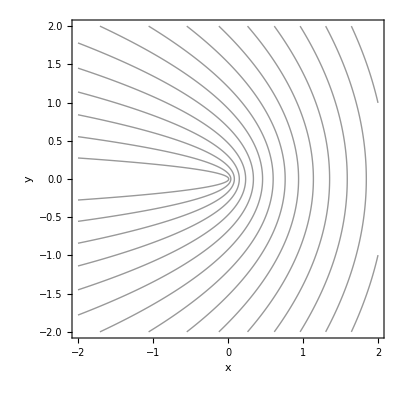

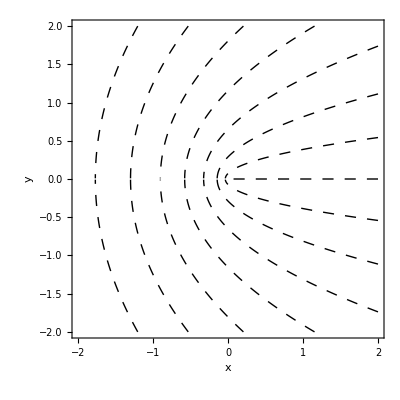

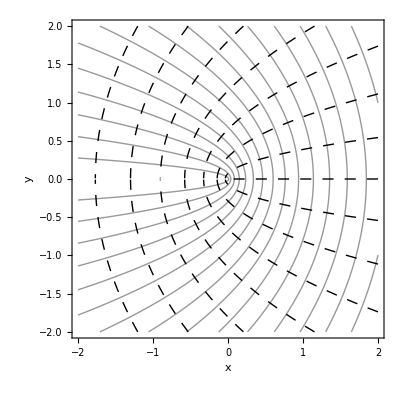

```mathematica
z=x+ⅈ*y;w[z_]:=√z;
real=ComplexExpand[Re[w[z]]]
imaginary=ComplexExpand[Im[w[z]]]
field=ContourPlot[real,{x,-2,2},{y,-2,2},ContourShading->False,PlotPoints->100,Contours->15,Axes->True,AxesLabel->{"x","y"}]
potential=ContourPlot[imaginary,{x,-2,2},{y,-2,2},ContourShading->False,PlotPoints->100,Contours->15,Axes->True,ContourStyle->Dashing[{0.02,0.02}],AxesLabel->{"x","y"}]
Show[field,potential]
```